# TP 4 : Restauration d’image

## Travail en séance : Camille LANFREDI

## Calcul de variations totales

Question 1.

```mathematica
x={{1,2,3},{4,5,6},{7,8,9}}
MatrixForm[x]
x'=MatrixForm[RotateLeft[x]]
x'' = MatrixForm[Transpose[RotateLeft[Transpose[x]]]]
```

{{1,2,3},{4,5,6},{7,8,9}}

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

(4 | 5 | 6
7 | 8 | 9
1 | 2 | 3)

(2 | 3 | 1
5 | 6 | 4
8 | 9 | 7)

Question 2.

```mathematica
variationTotale[x_]:=(Norm[x-RotateLeft[x],"Frobenius"]^2+Norm[x-Transpose[RotateLeft[Transpose[x]]],"Frobenius"]^2)/2
```

Question 3.

```mathematica
(* Constante globale *)
n = 200;
imageUniforme:=RandomReal[1,{n,n}]
Image[imageUniforme]
variationTotale[imageUniforme]
```

-Graphics-

6703.33

Question 4.

```mathematica
image=-Graphics-;
```

```mathematica
data=ImageData[image]
```

```mathematica
variationTotale[data]
```

706.62

Question 5.

```mathematica
σ=0.1;
a0=mat+RandomVariate[NormalDistribution[0,σ],Dimensions[mat]]
```

```mathematica
Image[a0]
variationTotale[a0]
```

-Graphics-

1504.61

Question 6.

## Minimisation par méthode du gradient

```mathematica
(* Constantes globales *)
μ = 0.01;
λ = 10;
```

Question 7.

```mathematica
nextStep[x_]:= x -μ*((4+λ) *x-RotateLeft[x]-Transpose[RotateLeft[Transpose[x]]]-RotateRight[x]-Transpose[RotateRight[Transpose[x]]]-λ*a0)
```

Question 8.

```mathematica
pointsIntermediares = NestList[nextStep,a0,60]
```

Question 9.

```mathematica
Manipulate[Image[pointsIntermediares[[k]]],{k,1,60,1}]
```

Question 10.

```mathematica
Manipulate[{k,variationTotale[pointsIntermediares[[k]]]},{k,1,60,1}]
```

Question 11.

```mathematica
f[x_]:= variationTotale[x]+(λ/2)*Norm[x-a0, "Frobenius"];
```

Question 12.

```mathematica
μ2 = 0.05;
λ2 = 20;
nextStep2[x_]:= x -μ2*((4+λ2) *x-RotateLeft[x]-Transpose[RotateLeft[Transpose[x]]]-RotateRight[x]-Transpose[RotateRight[Transpose[x]]]-λ2*a0)
pointsIntermediares2 = NestList[nextStep2,a0,60]
```

## S’il vous reste du temps

Évaluer tout d’abord la cellule suivante.

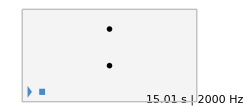

```mathematica
(* fréquence d'échantillonnage *)
freq = 2000;
(* produit une note à la fréquence ξ pendant t secondes *)
note[ξ_,t_]:=Table[Sin[2π ξ k],{k,0.,t,1/freq}];
(* Diverses fréquences *)
D4=293.665;
E4=329.628;
Fsharp4=369.994;
G4=391.995;
A4=440;
(* signal non bruité *)
audio = Flatten[{note[Fsharp4,1], note[Fsharp4,1],note[G4,1], note[A4,1],note[A4,1],note[G4,1],note[Fsharp4,1],note[E4,1],note[D4,1],note[D4,1],note[E4,1],note[Fsharp4,1], note[Fsharp4,3/2],note[E4,1/2],note[E4,1]}];
n = Length[audio];
(* génération du bruit *)
σ=0.1;
bruit=RandomReal[NormalDistribution[0,σ],n];
(* signal à restaurer *)
a0 = audio + bruit;
(* émission du signal *)
Sound[SampledSoundList[a0,freq]]
```

```mathematica
variationTotaleAudio [x_]:=Sum[(x[[k]]-x[[k+1]])^2,{k,200}]
```

```mathematica
variationTotaleAudio[a0]
```

Question 14

```mathematica
(* Définition de la fonction de coût *)
variationTotaleAudio[x_List] := Total[(x - RotateRight[x])^2];

(* Algorithme de descente de gradient *)
gradientDescent[a0_List, learningRate_, maxIterations_, tolerance_] := Module[{x, xNew, iteration},
  x = a0;
  iteration = 0;
  cost = variationTotaleAudio[x];
  While[iteration < maxIterations,
    gradient = 2*(x - RotateRight[x]);
    xNew = x - learningRate*gradient;
    newCost = variationTotaleAudio[xNew];
    If[Abs[cost - newCost] < tolerance, Break[]];
    x = xNew;
    cost = newCost;
    iteration++;
  ];
  Return[x];
];

(* Paramètres *)
learningRate = 0.01;
maxIterations = 1000;
tolerance = 1*^-6;

(* Restauration du signal audio *)
restoredSignal = gradientDescent[a0, learningRate, maxIterations, tolerance];

(* Émission du signal restauré *)
Sound[SampledSoundList[restoredSignal, freq]]
```